## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
Needs["Toolbox`"];
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="G3PD2";
fitLabel=rxnName;
dataFileName=rxnName;
KeqEquilibrator=2.4*10^-5;

assumedUncertaintyFraction = 0.05;
removeInputFiles = False;
removeOutputFiles = True;
(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "fit_G3PD2";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath, assumedUncertaintyFraction];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

ordered bi bi; [nadp,glyc3p,dhap,nadph]

Structure:

Active sites:

Km Values:

Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
nadph | 3.4×10^-6 | 3.23×10^-6
3.57×10^-6 |  | M | 7.4 | 23 | trishcl | 0.1 | 
dhap | 0.00018 | 0.000171
0.000189 |  | M | 7.4 | 23 | trishcl | 0.1 | 
nadp | 0.000165 | 0.00015675
0.00017325 |  | M | 7.4 | 23 | trishcl | 0.1 | 
glyc3p | 0.00003 | 0.0000285
0.0000315 |  | M | 7.4 | 23 | trishcl | 0.1 |

S0.5 Values:

Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kic | glyc3p | 4.2×10^-6 | 3.99×10^-6
4.41×10^-6 | nadph | 0.0001 | Competitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
Kincu | glyc3p | 6.5×10^-6 | 6.175×10^-6
6.825×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
Kincc | glyc3p | 2.5×10^-6 | 2.375×10^-6
2.625×10^-6 | dhap | 0.0001 | NonCompetitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
Kincu | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
Kincc | nadp | 0.0013 | 0.001235
0.001365 | nadph | 0.00001 | NonCompetitive | dhap | 0.00018 | M | 7.4 | 23 | trishcl | 0.1 | 
Kic | nadp | 0.000187 | 0.00017765
0.00019635 | dhap | 0.002 | Competitive | nadph | 3.4×10^-6 | M | 7.4 | 23 | trishcl | 0.1 | 
Kic | dhap | 0.000038 | 0.0000361
0.0000399 | nadp | 0.002 | Competitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
Kincu | dhap | 0.00024 | 0.000228
0.000252 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
Kincc | dhap | 0.00012 | 0.000114
0.000126 | glyc3p | 0.0001 | NonCompetitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 | 
Kincu | nadph | 8.×10^-7 | 7.6×10^-7
8.4×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
Kincc | nadph | 6.×10^-7 | 5.7×10^-7
6.3×10^-7 | nadp | 0.0001 | NonCompetitive | glyc3p | 0.00003 | M | 7.4 | 23 | trishcl | 0.1 | 
Kic | nadph | 4.×10^-7 | 3.8×10^-7
4.2×10^-7 | glyc3p | 0.0002 | Competitive | nadp | 0.000165 | M | 7.4 | 23 | trishcl | 0.1 |

Activation Values:

Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Construct enzyme module

(glyc3p^c+nadp^c⇌dhap^c+h^c+nadph^c)^G3PD2

```mathematica
{{"ordered bi bi"}, {"\"[nadp,glyc3p,dhap,nadph]\""}}
```

```mathematica
catalyticBranch={"E_G3PD2[c] + nadp[c] <=> E_G3PD2[c]&nadp",
				"E_G3PD2[c]&nadp + glyc3p[c] <=> E_G3PD2[c]&nadp&glyc3p",
				"E_G3PD2[c]&nadp&glyc3p <=> E_G3PD2[c]&nadph&dhap",
				"E_G3PD2[c]&nadph&dhap <=> E_G3PD2[c]&nadph + dhap[c]",
				"E_G3PD2[c]&nadph <=> E_G3PD2[c] + nadph[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites-> 0];
enzymeModel["Reactions"]
nActiveSites=1;
```

{((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,((G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c)^G3PD22,((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,((G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c)^G3PD24,((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((G3PD2^c)_^+nadp^c⇌(G3PD2^c&nadp^c)_^)^G3PD21,Overscript[(G3PD2^c&nadph^c)_^⇌(G3PD2^c)_^+nadph^c, G3PD22],((G3PD2^c&nadp^c)_^+glyc3p^c⇌(G3PD2^c&nadp^c&glyc3p^c)_^)^G3PD23,Overscript[(G3PD2^c&nadph^c&dhap^c)_^⇌(G3PD2^c&nadph^c)_^+dhap^c, G3PD24],((G3PD2^c&nadp^c&glyc3p^c)_^⇌(G3PD2^c&nadph^c&dhap^c)_^)^G3PD25};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

#### Define some parameters

```mathematica
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={{"prod_inhib_dhap", nadph^c->0},{"prod_inhib_nadph", dhap^c->0}};
otherMetsForwardZeroSub={{"prod_inhib_glyc3p", nadp^c->0},{"prod_inhib_nadp", glyc3p^c->0}};
```

```mathematica
{haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub,
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, {inhibitionList[2]}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  simplifyMaxTime, nActiveSites];;
```

kcat for

kcat rev

km for

km rev

```mathematica
trueRes={{((G3PD2^c&nadph^c)_^+glyc3p^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_Kincu_glyc3p_1_nadph}, {((G3PD2^c)_^+glyc3p^c⇌(G3PD2^c&glyc3p^c)_^)^G3PD2_Kincc_glyc3p_1_nadph}, {((G3PD2^c&glyc3p^c)_^+nadph^c⇌(G3PD2^c&nadph^c&glyc3p^c)_^)^G3PD2_NC_glyc3p}, {((G3PD2^c&nadp^c)_^+dhap^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_Kincu_dhap_1_nadp}, {((G3PD2^c)_^+dhap^c⇌(G3PD2^c&dhap^c)_^)^G3PD2_Kincc_dhap_1_nadp}, {((G3PD2^c&dhap^c)_^+nadp^c⇌(G3PD2^c&nadp^c&dhap^c)_^)^G3PD2_NC_dhap}};
```

```mathematica
SameQ[trueRes, nonCatalyticReactions]
```

False

## Semi-Automated Simulate Data

```mathematica
haldaneDataList=Table[
	{haldaneRatio, KeqEquilibrator,{0.9*KeqEquilibrator,1.1*KeqEquilibrator}},
{haldaneRatio, haldaneRatiosList}];

customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Export["G3PD2SimulateDataArguments.mx",{enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];
Export["G3PD2SimulateDataResults.mx",{allFittingData, dataPath, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
Get["MASSef`"];

{allFittingData, dataPath, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.0423023,0.0423023,0.0423023,0.0423023}

```mathematica
FilePrint@dataPath
```

dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	paramG3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0.01	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.09090909090909097
0.01	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.1368068886032101
0.01	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.20076000891310194
0.01	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.2847472489508014
0.01	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.386863179846857
0.01	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.5000000000000001
0.01	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.6131368201531433
0.01	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7152527510491989
0.01	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7992399910868982
0.01	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.86319311139679
0.01	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.9090909090909091
0.000018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.09090909090909098
0.00002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.13680688860321016
0.00004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.200760008913102
0.00007165929069962952	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.28474724895080145
0.00011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.38686317984685703
0.00018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.5000000000000002
0.0002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.6131368201531433
0.0004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7152527510491989
0.0007165929069962958	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7992399910868984
0.0011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.86319311139679
0.0018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.9090909090909092
0	0.01	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.09090909090909097
0	0.01	0.000026150737675608408	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.13680688860321016
0	0.01	0.000041446126119908146	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.20076000891310203
0	0.01	0.00006568768314132706	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.2847472489508014
0	0.01	0.00010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.3868631798468571
0	0.01	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.5000000000000002
0	0.01	0.0002615073767560841	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.6131368201531434
0	0.01	0.0004144612611990815	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7152527510491989
0	0.01	0.0006568768314132713	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7992399910868985
0	0.01	0.0010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.8631931113967901
0	0.01	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.9090909090909092
0	3.0000000000000013e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.09090909090909094
0	4.7546795773833446e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.1368068886032101
0	7.535659294528749e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.20076000891310194
0	0.000011943215116604912	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.28474724895080133
0	0.000018928720334405797	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.3868631798468569
0	0.00003000000000000001	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.5000000000000001
0	0.00004754679577383344	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.6131368201531432
0	0.00007535659294528749	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7152527510491988
0	0.00011943215116604925	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7992399910868984
0	0.00018928720334405796	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.86319311139679
0	0.00030000000000000014	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.9090909090909091
0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.06250000000000006
0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.17411239489546845
0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.4000000000000002
0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6782688399674107
0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.8695652173913044
0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.047619047619047665
0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.13652705949581442
0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.33333333333333354
0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6125741132772071
0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.8333333333333335
0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.032258064516129066
0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.09535767393826004
0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2500000000000002
0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5131670194948622
0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.7692307692307694
0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.04914933837429115
0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.1359715179829786
0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.3080568720379148
0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5136142175737065
0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6509764646970455
0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.03367875647668395
0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.09481652165128764
0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.22260273972602748
0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.3879359014999326
0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5070202808112324
0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.0206677265500795
0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.059062933642962216
0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.14317180616740097
0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2604666499256048
0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.351541373715522
0.000018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.06060606060606066
0.000056920997883030876	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.16016871556802817
0.00018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.3333333333333335
0.0005692099788303088	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.5064979510986386
0.0018000000000000017	0	0.00065	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.6060606060606061
0.000018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.04545454545454549
0.000056920997883030876	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.12012653667602116
0.00018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.2500000000000001
0.0005692099788303088	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.379873463323979
0.0018000000000000017	0	0.0013	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.4545454545454546
0.000018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.03030303030303033
0.000056920997883030876	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.08008435778401408
0.00018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.16666666666666674
0.0005692099788303088	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.2532489755493193
0.0018000000000000017	0	0.0026	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.30303030303030304
0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.06250000000000003
0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.1741123948954684
0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.40000000000000013
0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.6782688399674105
0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.8695652173913044
0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.047619047619047644
0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.1365270594958144
0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.3333333333333334
0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.612574113277207
0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.8333333333333334
0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.032258064516129045
0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.09535767393826002
0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.2500000000000001
0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.5131670194948621
0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.7692307692307694
0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.06250000000000003
0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.17411239489546837
0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.40000000000000013
0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.6782688399674105
0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.8695652173913044
0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.04761904761904764
0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.13652705949581434
0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3333333333333334
0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.612574113277207
0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.8333333333333335
0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.032258064516129045
0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.09535767393826
0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.25000000000000006
0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.5131670194948622
0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.7692307692307693
0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.052980132450331174
0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.1447390418373348
0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3200000000000002
0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.518564992170751
0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.6451612903225806
0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.03738317757009349
0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.10356583218373844
0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.235294117647059
0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.39361254767503817
0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.5000000000000001
0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.023529411764705903
0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.06601047571169773
0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.1538461538461539
0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.26561052385648354
0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3448275862068966
0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.057901085645355864
0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.15517252975139625
0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.33103448275862074
0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.5159442342521813
0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6266318537859008
0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.042477876106194704
0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.11459214550830052
0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.2474226804123712
0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.39060056309756436
0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.47808764940239046
0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.02771362586605082
0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.07523930500173176
0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.16438356164383564
0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.2628747818212248
0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.32432432432432434
0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.06250000000000006
0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.17411239489546848
0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.4000000000000002
0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6782688399674106
0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.8695652173913045
0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.047619047619047665
0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.13652705949581445
0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.33333333333333354
0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6125741132772071
0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.8333333333333335
0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.03225806451612906
0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.09535767393826007
0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.25000000000000017
0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.5131670194948623
0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.7692307692307693

### Sanity check plots

```mathematica
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
assumedSaturatingConc=0.01;
eTotal=1;
logStepSize=0.5;
inhibFittingData=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  inhibitionList, kmList, assumedSaturatingConc, eTotal,
			   logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList];
```

#### C inhib of dhap by glyc3p

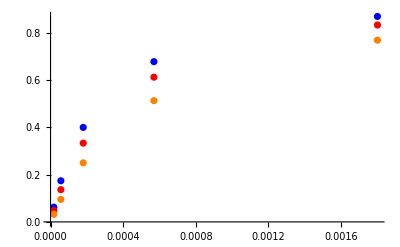

```mathematica
inhib1=inhibFittingData[[1;;5,{1,-1}]];
inhib2=inhibFittingData[[6;;10,{1,-1}]];
inhib3=inhibFittingData[[11;;15,{1,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.00027}

{1.,0.00036}

{1.,0.00054}

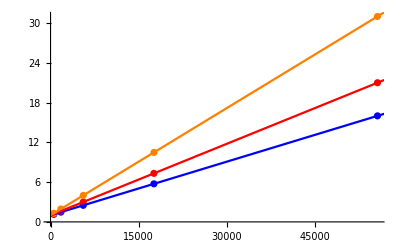

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,100000}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of nadph by glyc3p

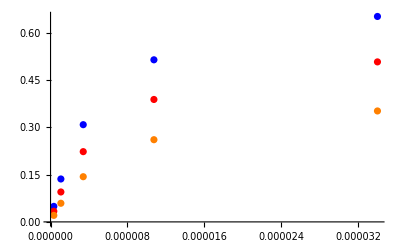

```mathematica
inhib1=inhibFittingData[[16;;20,{4,-1}]];
inhib2=inhibFittingData[[21;;25,{4,-1}]];
inhib3=inhibFittingData[[26;;30,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.34615,6.46×10^-6}

{1.69231,9.52×10^-6}

{2.38462,0.00001564}

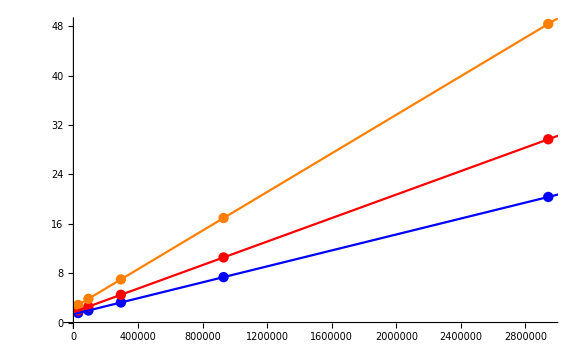

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of dhap by nadp

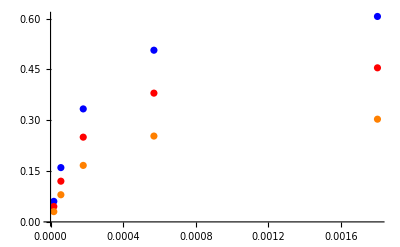

```mathematica
inhib1=inhibFittingData[[31;;35,{1,-1}]];
inhib2=inhibFittingData[[36;;40,{1,-1}]];
inhib3=inhibFittingData[[41;;45,{1,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.5,0.00027}

{2.,0.00036}

{3.,0.00054}

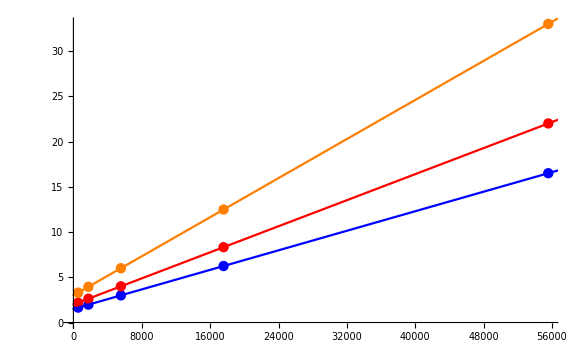

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of nadph by nadp

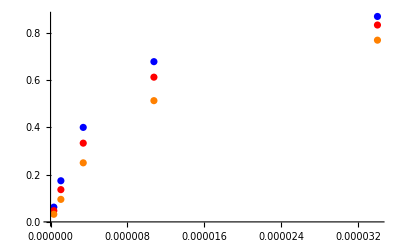

```mathematica
inhib1=inhibFittingData[[46;;50,{4,-1}]];
inhib2=inhibFittingData[[51;;55,{4,-1}]];
inhib3=inhibFittingData[[56;;60,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,5.1×10^-6}

{1.,6.8×10^-6}

{1.,0.0000102}

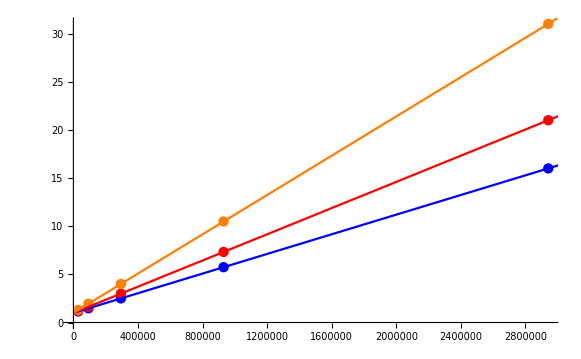

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of glyc3p by dhap

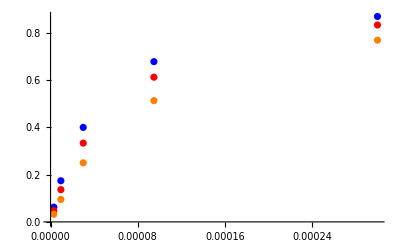

```mathematica
inhib1=inhibFittingData[[61;;65,{2,-1}]];
inhib2=inhibFittingData[[66;;70,{2,-1}]];
inhib3=inhibFittingData[[71;;75,{2,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.000045}

{1.,0.00006}

{1.,0.00009}

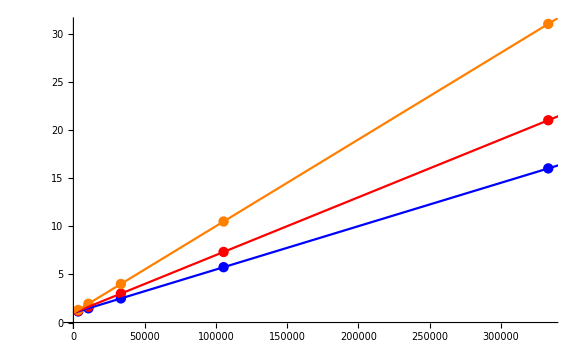

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### NC inhib of nadp by dhap

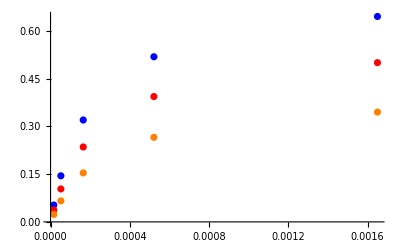

```mathematica
inhib1=inhibFittingData[[76;;80,{3,-1}]];
inhib2=inhibFittingData[[81;;85,{3,-1}]];
inhib3=inhibFittingData[[86;;90,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.375,0.00028875}

{1.75,0.0004125}

{2.5,0.00066}

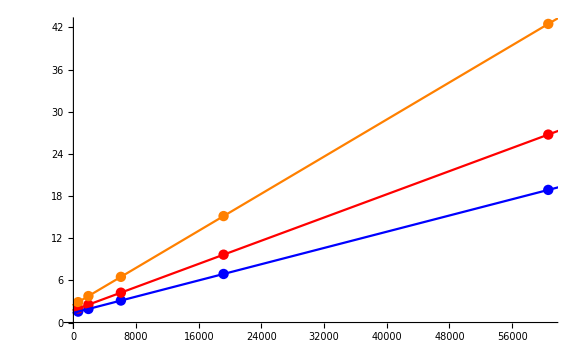

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

#### C inhib of nadp by nadph

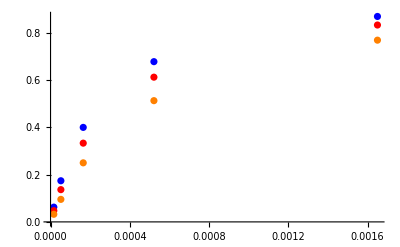

```mathematica
inhib1=inhibFittingData[[106;;110,{3,-1}]];
inhib2=inhibFittingData[[111;;115,{3,-1}]];
inhib3=inhibFittingData[[116;;120,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.0002475}

{1.,0.00033}

{1.,0.000495}

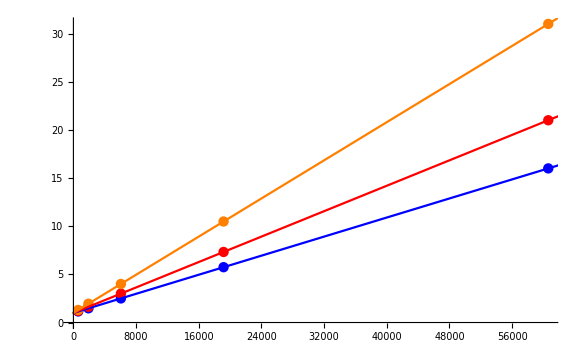

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

### Simulate data with uncertainty

```mathematica
Export["G3PD2SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, KeqName,allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];

Export["G3PD2SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, KeqName,allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.0423023,0.0423023,0.0423023,0.0423023}

{0.0423023,0.0423023,0.0423023,0.0423023}

{0.0423023,0.0423023,0.0423023,0.0423023}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000022779994792933335
0.01	0	0	3.129037597873447e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.09090909090909094
0.01	0	0	4.959190387824503e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.13680688860321008
0.01	0	0	7.859787085781648e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.20076000891310197
0.01	0	0	1.2456923046449087e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.28474724895080133
0.01	0	0	1.9742892535329122e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.386863179846857
0.01	0	0	3.129037597873447e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.5000000000000001
0.01	0	0	4.959190387824503e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.6131368201531433
0.01	0	0	7.859787085781647e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7152527510491989
0.01	0	0	0.000012456923046449087	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7992399910868981
0.01	0	0	0.00001974289253532912	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.8631931113967899
0.01	0	0	0.000031290375978734474	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.9090909090909092
0.000020410217358979325	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.09090909090909095
0.00003234801454889799	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.1368068886032101
0.0000512681480481815	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.20076000891310194
0.00008125453883165142	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.2847472489508017
0.0001287797654508513	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.386863179846857
0.00020410217358979323	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.5000000000000001
0.0003234801454889799	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.6131368201531432
0.000512681480481815	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7152527510491988
0.0008125453883165134	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7992399910868985
0.0012877976545085132	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.86319311139679
0.0020410217358979325	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.9090909090909092
0	0.01	0.000015596983927693493	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.0909090909090909
0	0.01	0.000024719553649926826	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.13680688860321003
0	0.01	0.00003917785230044631	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.20076000891310186
0	0.01	0.00006209271140622423	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.2847472489508012
0	0.01	0.00009841031560917736	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.3868631798468568
0	0.01	0.00015596983927693492	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.4999999999999999
0	0.01	0.00024719553649926826	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.6131368201531431
0	0.01	0.0003917785230044631	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7152527510491987
0	0.01	0.000620927114062243	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7992399910868982
0	0.01	0.0009841031560917737	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.8631931113967899
0	0.01	0.0015596983927693491	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.9090909090909091
0	3.0156248333855526e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.09090909090909087
0	4.779443269449444e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.13680688860321
0	7.574907101504514e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.20076000891310183
0	0.000012005418698699829	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.28474724895080117
0	0.00001902730636821473	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.38686317984685675
0	0.000030156248333855528	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.49999999999999983
0	0.00004779443269449444	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.6131368201531431
0	0.00007574907101504515	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7152527510491987
0	0.00012005418698699842	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7992399910868981
0	0.00019027306368214728	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.8631931113967898
0	0.0003015624833385553	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.9090909090909091
0.000018000000000000017	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.06250000000000006
0.000056920997883030876	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.17411239489546845
0.00018000000000000017	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.4000000000000002
0.0005692099788303088	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6782688399674107
0.0018000000000000017	2.1037538999529466e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.8695652173913044
0.000018000000000000017	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.047619047619047665
0.000056920997883030876	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.13652705949581442
0.00018000000000000017	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.33333333333333354
0.0005692099788303088	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6125741132772071
0.0018000000000000017	4.207507799905893e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.8333333333333335
0.000018000000000000017	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.032258064516129066
0.000056920997883030876	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.09535767393826004
0.00018000000000000017	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2500000000000002
0.0005692099788303088	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5131670194948622
0.0018000000000000017	8.415015599811786e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.7692307692307694
0.0001	2.323100334937473e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.04836455105829019
0.0001	2.323100334937473e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.13412625445262563
0.0001	2.323100334937473e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.30535015151655454
0.0001	2.323100334937473e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5120681925411658
0.0001	2.323100334937473e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6515542596641035
0.0001	4.646200669874946e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.03294610527941429
0.0001	4.646200669874946e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.09303151126927353
0.0001	4.646200669874946e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2197871000642933
0.0001	4.646200669874946e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.38617463369541344
0.0001	4.646200669874946e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5077216373944418
0.0001	9.292401339749893e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.020118618276724343
0.0001	9.292401339749893e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.057684050662945886
0.0001	9.292401339749893e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.14085072169558133
0.0001	9.292401339749893e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2588811572461585
0.0001	9.292401339749893e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.35221606247258225
0.000018000000000000017	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.060700691713789376
0.000056920997883030876	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.16032676902440174
0.00018000000000000017	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.33332965124202485
0.0005692099788303088	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.5059879589805726
0.0018000000000000017	0	0.0006418803472088958	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.6051038933232198
0.000018000000000000017	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.04556108862970446
0.000056920997883030876	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.12030443458869829
0.00018000000000000017	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.2499958576701565
0.0005692099788303088	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.379300010895401
0.0018000000000000017	0	0.0012837606944177916	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.45347000155804146
0.000018000000000000017	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.030397809400099635
0.000056920997883030876	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.08024256736057825
0.00018000000000000017	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.166662984616031
0.0005692099788303088	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.2527394964251104
0.0018000000000000017	0	0.002567521388835583	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.30207509815642164
0.002	0	0.00009610879322718565	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.06250000000000003
0.002	0	0.00009610879322718565	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.1741123948954684
0.002	0	0.00009610879322718565	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.40000000000000013
0.002	0	0.00009610879322718565	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.6782688399674105
0.002	0	0.00009610879322718565	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.8695652173913044
0.002	0	0.0001922175864543713	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.047619047619047644
0.002	0	0.0001922175864543713	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.1365270594958144
0.002	0	0.0001922175864543713	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.3333333333333334
0.002	0	0.0001922175864543713	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.612574113277207
0.002	0	0.0001922175864543713	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.8333333333333334
0.002	0	0.0003844351729087426	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.032258064516129045
0.002	0	0.0003844351729087426	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.09535767393826002
0.002	0	0.0003844351729087426	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.2500000000000001
0.002	0	0.0003844351729087426	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.5131670194948621
0.002	0	0.0003844351729087426	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.7692307692307694
0.00001900948058623012	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.06250000000000003
0.00001900948058623012	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.17411239489546837
0.00001900948058623012	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.40000000000000013
0.00001900948058623012	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.6782688399674105
0.00001900948058623012	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.8695652173913044
0.00003801896117246024	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.04761904761904764
0.00003801896117246024	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.13652705949581434
0.00003801896117246024	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3333333333333334
0.00003801896117246024	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.612574113277207
0.00003801896117246024	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.8333333333333335
0.00007603792234492048	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.032258064516129045
0.00007603792234492048	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.09535767393826
0.00007603792234492048	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.25000000000000006
0.00007603792234492048	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.5131670194948622
0.00007603792234492048	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.7692307692307693
0.00008801172619308182	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.05392826850725052
0.00008801172619308182	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.1468363738317205
0.00008801172619308182	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3225755387735473
0.00008801172619308182	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.5190048718043427
0.00008801172619308182	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.6427813699588212
0.00017602345238616364	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.038334296563139955
0.00017602345238616364	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.10572695809169022
0.00017602345238616364	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.23808967437456838
0.00017602345238616364	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3941196390597012
0.00017602345238616364	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.49714690924781946
0.0003520469047723273	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.024287996139776148
0.0003520469047723273	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.06777651318297108
0.0003520469047723273	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.15624520784590168
0.0003520469047723273	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.26607254788615603
0.0003520469047723273	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.34211944939784794
0	3.0000000000000013e-6	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.058215630659585585
0	9.486832980505141e-6	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.1557909715555081
0	0.00003000000000000001	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.331491327638692
0	0.00009486832980505142	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.5152503366919886
0	0.00030000000000000014	0.0001	3.4658817516561726e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6247713872558774
0	3.0000000000000013e-6	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.042817320600216896
0	9.486832980505141e-6	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.11526797199910761
0	0.00003000000000000001	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.24793345347921777
0	0.00009486832980505142	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.38980571274173864
0	0.00030000000000000014	0.0001	6.931763503312345e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.47592510815726297
0	3.0000000000000013e-6	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.028003306287614074
0	9.486832980505141e-6	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.07582308326398883
0	0.00003000000000000001	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.16483478398700885
0	0.00009486832980505142	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.2621552635757265
0	0.00030000000000000014	0.0001	1.386352700662469e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.32233714013317194
0	0.0002	0.000016500000000000015	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.06250000000000006
0	0.0002	0.000052177581392778313	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.17411239489546848
0	0.0002	0.00016500000000000016	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.4000000000000002
0	0.0002	0.0005217758139277831	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6782688399674106
0	0.0002	0.0016500000000000017	2.1280015897898585e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.8695652173913045
0	0.0002	0.000016500000000000015	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.047619047619047665
0	0.0002	0.000052177581392778313	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.13652705949581445
0	0.0002	0.00016500000000000016	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.33333333333333354
0	0.0002	0.0005217758139277831	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6125741132772071
0	0.0002	0.0016500000000000017	4.256003179579717e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.8333333333333335
0	0.0002	0.000016500000000000015	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.03225806451612906
0	0.0002	0.000052177581392778313	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.09535767393826007
0	0.0002	0.00016500000000000016	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.25000000000000017
0	0.0002	0.0005217758139277831	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.5131670194948623
0	0.0002	0.0016500000000000017	8.512006359159434e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.7692307692307693

### Parameter scan

```mathematica
Export["G3PD2ParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList}, "MX"];

Export["G3PD2ParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
Get["MASSef`"];
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",4,{0.01,10,100}},
				{"inhib",1,{0.01,1,100}},
				{"inhib",2,{10^-8,10.^-6,10^-4}},
				{"inhib",4,{10^-8,10.^-6,10^-4}},
				{"inhib",5,{10^-8,10.^-6,10^-4}},
				{"inhib",7,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, eqRateConstSub, customRatiosDataList];
```

{0.0423023,0.0423023,0.0423023,0.0423023}

{0.0423023,0.0423023,0.0423023,0.0423023}

{0.0423023,0.0423023,0.0423023,0.0423023}

«21 more identical outputs»

```mathematica
FilePrint@dataPathList[[16]]
```

dhap[c]	glyc3p[c]	nadp[c]	nadph[c]	param_G3PD2_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt"	0.000024
0.01	0	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.09090909090909097
0.01	0	0	5.388636854367791e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.1368068886032101
0.01	0	0	8.540413867132584e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.20076000891310194
0.01	0	0	1.3535643798818904e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.2847472489508014
0.01	0	0	2.1452549712326573e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.386863179846857
0.01	0	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.5000000000000001
0.01	0	0	5.388636854367791e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.6131368201531433
0.01	0	0	8.540413867132584e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7152527510491989
0.01	0	0	0.000013535643798818902	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.7992399910868982
0.01	0	0	0.000021452549712326573	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.86319311139679
0.01	0	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt"	0.9090909090909091
0.000018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.09090909090909098
0.00002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.13680688860321016
0.00004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.200760008913102
0.00007165929069962952	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.28474724895080145
0.00011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.38686317984685703
0.00018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.5000000000000002
0.0002852807746430008	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.6131368201531433
0.0004521395576717252	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7152527510491989
0.0007165929069962958	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.7992399910868984
0.0011357232200643484	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.86319311139679
0.0018000000000000017	0	0	0.01	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt"	0.9090909090909092
0	0.01	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.09090909090909097
0	0.01	0.000026150737675608408	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.13680688860321016
0	0.01	0.000041446126119908146	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.20076000891310203
0	0.01	0.00006568768314132706	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.2847472489508014
0	0.01	0.00010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.3868631798468571
0	0.01	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.5000000000000002
0	0.01	0.0002615073767560841	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.6131368201531434
0	0.01	0.0004144612611990815	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7152527510491989
0	0.01	0.0006568768314132713	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.7992399910868985
0	0.01	0.0010410796183923194	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.8631931113967901
0	0.01	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt"	0.9090909090909092
0	3.0000000000000013e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.09090909090909094
0	4.7546795773833446e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.1368068886032101
0	7.535659294528749e-6	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.20076000891310194
0	0.000011943215116604912	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.28474724895080133
0	0.000018928720334405797	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.3868631798468569
0	0.00003000000000000001	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.5000000000000001
0	0.00004754679577383344	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.6131368201531432
0	0.00007535659294528749	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7152527510491988
0	0.00011943215116604925	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.7992399910868984
0	0.00018928720334405796	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.86319311139679
0	0.00030000000000000014	0.01	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt"	0.9090909090909091
0.000018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.06250000000000006
0.000056920997883030876	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.17411239489546845
0.00018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.4000000000000002
0.0005692099788303088	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6782688399674107
0.0018000000000000017	2.1e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.8695652173913044
0.000018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.047619047619047665
0.000056920997883030876	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.13652705949581442
0.00018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.33333333333333354
0.0005692099788303088	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6125741132772071
0.0018000000000000017	4.2e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.8333333333333335
0.000018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.032258064516129066
0.000056920997883030876	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.09535767393826004
0.00018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2500000000000002
0.0005692099788303088	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5131670194948622
0.0018000000000000017	8.4e-6	0	0.0001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.7692307692307694
0.0001	2.25e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.04914933837429115
0.0001	2.25e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.1359715179829786
0.0001	2.25e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.3080568720379148
0.0001	2.25e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5136142175737065
0.0001	2.25e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.6509764646970455
0.0001	4.5e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.03367875647668395
0.0001	4.5e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.09481652165128764
0.0001	4.5e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.22260273972602748
0.0001	4.5e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.3879359014999326
0.0001	4.5e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.5070202808112324
0.0001	9.e-6	0	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.0206677265500795
0.0001	9.e-6	0	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.059062933642962216
0.0001	9.e-6	0	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.14317180616740097
0.0001	9.e-6	0	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.2604666499256048
0.0001	9.e-6	0	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt"	0.351541373715522
0.000018000000000000017	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003075621850474136
0.000056920997883030876	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003076430577952514
0.00018000000000000017	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003076686408555751
0.0005692099788303088	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003076767318151131
0.0018000000000000017	0	0.00032500249999999997	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00003076792904897357
0.000018000000000000017	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00001538071104117315
0.000056920997883030876	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.000015383137791949832
0.00018000000000000017	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.00001538390535730399
0.0005692099788303088	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.000015384148098722505
0.0018000000000000017	0	0.0006500049999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.000015384224861893246
0.000018000000000000017	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.691006132872779e-6
0.000056920997883030876	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.69181514517081e-6
0.00018000000000000017	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.692071012744457e-6
0.0005692099788303088	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.69215192871839e-6
0.0018000000000000017	0	0.0013000099999999999	0.00001	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	7.692177516950351e-6
0.002	0	0.0000935	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.06250000000000003
0.002	0	0.0000935	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.1741123948954684
0.002	0	0.0000935	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.40000000000000013
0.002	0	0.0000935	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.6782688399674105
0.002	0	0.0000935	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.8695652173913044
0.002	0	0.000187	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.047619047619047644
0.002	0	0.000187	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.1365270594958144
0.002	0	0.000187	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.3333333333333334
0.002	0	0.000187	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.612574113277207
0.002	0	0.000187	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.8333333333333334
0.002	0	0.000374	3.400000000000002e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.032258064516129045
0.002	0	0.000374	1.0751744044572496e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.09535767393826002
0.002	0	0.000374	3.4000000000000018e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.2500000000000001
0.002	0	0.000374	0.000010751744044572496	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.5131670194948621
0.002	0	0.000374	0.00003400000000000002	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt"	0.7692307692307694
0.000019	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.06250000000000003
0.000019	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.17411239489546837
0.000019	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.40000000000000013
0.000019	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.6782688399674105
0.000019	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.8695652173913044
0.000038	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.04761904761904764
0.000038	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.13652705949581434
0.000038	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3333333333333334
0.000038	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.612574113277207
0.000038	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.8333333333333335
0.000076	3.0000000000000013e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.032258064516129045
0.000076	9.486832980505141e-6	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.09535767393826
0.000076	0.00003000000000000001	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.25000000000000006
0.000076	0.00009486832980505142	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.5131670194948622
0.000076	0.00030000000000000014	0.002	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.7692307692307693
0.00009	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.052980132450331174
0.00009	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.1447390418373348
0.00009	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3200000000000002
0.00009	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.518564992170751
0.00009	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.6451612903225806
0.00018	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.03738317757009349
0.00018	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.10356583218373844
0.00018	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.235294117647059
0.00018	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.39361254767503817
0.00018	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.5000000000000001
0.00036	0.0001	0.000016500000000000015	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.023529411764705903
0.00036	0.0001	0.000052177581392778313	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.06601047571169773
0.00036	0.0001	0.00016500000000000016	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.1538461538461539
0.00036	0.0001	0.0005217758139277831	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.26561052385648354
0.00036	0.0001	0.0016500000000000017	0	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt"	0.3448275862068966
0	3.0000000000000013e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.057901085645355864
0	9.486832980505141e-6	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.15517252975139625
0	0.00003000000000000001	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.33103448275862074
0	0.00009486832980505142	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.5159442342521813
0	0.00030000000000000014	0.0001	3.5e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6266318537859008
0	3.0000000000000013e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.042477876106194704
0	9.486832980505141e-6	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.11459214550830052
0	0.00003000000000000001	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.2474226804123712
0	0.00009486832980505142	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.39060056309756436
0	0.00030000000000000014	0.0001	7.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.47808764940239046
0	3.0000000000000013e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.02771362586605082
0	9.486832980505141e-6	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.07523930500173176
0	0.00003000000000000001	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.16438356164383564
0	0.00009486832980505142	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.2628747818212248
0	0.00030000000000000014	0.0001	1.4e-6	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.32432432432432434
0	0.0002	0.000016500000000000015	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.06250000000000006
0	0.0002	0.000052177581392778313	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.17411239489546848
0	0.0002	0.00016500000000000016	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.4000000000000002
0	0.0002	0.0005217758139277831	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6782688399674106
0	0.0002	0.0016500000000000017	2.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.8695652173913045
0	0.0002	0.000016500000000000015	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.047619047619047665
0	0.0002	0.000052177581392778313	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.13652705949581445
0	0.0002	0.00016500000000000016	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.33333333333333354
0	0.0002	0.0005217758139277831	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.6125741132772071
0	0.0002	0.0016500000000000017	4.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.8333333333333335
0	0.0002	0.000016500000000000015	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.03225806451612906
0	0.0002	0.000052177581392778313	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.09535767393826007
0	0.0002	0.00016500000000000016	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.25000000000000017
0	0.0002	0.0005217758139277831	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.5131670194948623
0	0.0002	0.0016500000000000017	8.e-7	1	7.4	23	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt"	0.7692307692307693

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=1;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	18
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_glyc3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateFor_nadp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/relRateRev_nadph.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadph.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_glyc3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/prod_inhib_nadp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_G3PD2/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

best_fit: 2.91914995435
best_fit: 1.04897924636
best_fit: 1.01249180433
best_fit: 0.938261590057
best_fit: 0.838935927002

### Run Fitting on your Local System with uncertainty

```mathematica
Do[
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python",
						"\""<>runFitScriptPath <>"\"",
						 "\""<>psoParameterPath <>"\"",
						 "\""<>lmaParameterPath <>"\"", 
						"\""<> StringTake[psoTrialSummaryFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						"\""<> StringTake[psoResultsFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						 "\""<>StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt\"", ToString @numTrials, 
						"\""<>dataPathList[[datasetI]] <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"] ,

{datasetI, 1, Length@dataPathList}];
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
lmaResultsFileName="lmaResults_GAPD_2017531321_4.txt";
```

```mathematica
splitChar = If[$OperatingSystem == "Windows", "\\", "/"];

resultsFileName = StringSplit[lmaResultsFileName, splitChar][[-1]];
(*fittingData = Import[FileNameJoin[{inputPath, dataFileName<>".dat"}, OperatingSystem->$OperatingSystem]];*)

fittingData=Import[dataPathList[[4]]];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw",resultsFileName}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
haldaneRatio_1 | 0.00139906 | 1.95736×10^-6 | 0.321626 | 0.448311 | 0.44687
relRateFor_nad | 0.0740369 | 0.00548146 | 15.6737 | 0.0909091 | 0.0766603
relRateFor_nad | 0.0705865 | 0.00498245 | 15.0011 | 0.136807 | 0.116284
relRateFor_nad | 0.0657327 | 0.00432078 | 14.0458 | 0.20076 | 0.172562
relRateFor_nad | 0.0592748 | 0.0035135 | 12.7581 | 0.284747 | 0.248419
relRateFor_nad | 0.0512914 | 0.0026308 | 11.1395 | 0.386863 | 0.343768
relRateFor_nad | 0.0422715 | 0.00178688 | 9.27468 | 0.5 | 0.453627
relRateFor_nad | 0.0330603 | 0.00109299 | 7.32989 | 0.613137 | 0.568195
relRateFor_nad | 0.0245753 | 0.000603945 | 5.50155 | 0.715253 | 0.675903
relRateFor_nad | 0.0174702 | 0.000305208 | 3.94283 | 0.79924 | 0.767727
relRateFor_nad | 0.0119809 | 0.000143541 | 2.72099 | 0.863193 | 0.839706
relRateFor_nad | 0.0079981 | 0.0000639697 | 1.82478 | 0.909091 | 0.892502
relRateFor_g3p | 0.255805 | 0.0654361 | 44.5125 | 0.0909091 | 0.0504432
relRateFor_g3p | 0.245933 | 0.0604833 | 43.2368 | 0.136807 | 0.0776559
relRateFor_g3p | 0.231794 | 0.0537283 | 41.3583 | 0.20076 | 0.117729
relRateFor_g3p | 0.212496 | 0.0451547 | 38.6939 | 0.284747 | 0.174567
relRateFor_g3p | 0.187817 | 0.0352751 | 35.1092 | 0.386863 | 0.251039
relRateFor_g3p | 0.158729 | 0.0251947 | 30.6141 | 0.5 | 0.34693
relRateFor_g3p | 0.127552 | 0.0162694 | 25.4499 | 0.613137 | 0.457094
relRateFor_g3p | 0.0973507 | 0.00947716 | 20.0811 | 0.715253 | 0.571622
relRateFor_g3p | 0.0708341 | 0.00501748 | 15.0495 | 0.79924 | 0.678958
relRateFor_g3p | 0.049498 | 0.00245005 | 10.7718 | 0.863193 | 0.770211
relRateFor_g3p | 0.0335125 | 0.00112309 | 7.42633 | 0.909091 | 0.841579
relRateFor_pi | 0.183693 | 0.0337429 | 52.6485 | 0.0909091 | 0.138771
relRateFor_pi | 0.172299 | 0.0296871 | 48.696 | 0.136807 | 0.203426
relRateFor_pi | 0.156907 | 0.0246197 | 43.5181 | 0.20076 | 0.288127
relRateFor_pi | 0.137487 | 0.0189027 | 37.242 | 0.284747 | 0.390793
relRateFor_pi | 0.114988 | 0.0132223 | 30.3132 | 0.386863 | 0.504134
relRateFor_pi | 0.0913515 | 0.0083451 | 23.4103 | 0.5 | 0.617052
relRateFor_pi | 0.0689349 | 0.00475203 | 17.202 | 0.613137 | 0.718608
relRateFor_pi | 0.0496499 | 0.00246511 | 12.1114 | 0.715253 | 0.80188
relRateFor_pi | 0.0344062 | 0.00118379 | 8.2446 | 0.79924 | 0.865134
relRateFor_pi | 0.0231473 | 0.000535798 | 5.47446 | 0.863193 | 0.910448
relRateFor_pi | 0.0152432 | 0.000232356 | 3.57221 | 0.909091 | 0.941566
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
absRateFor | 2.66256×10^-6 | 7.08925×10^-12 | 0.000613076 | 269.988 | 269.986
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
KdRatio_nad | 0.143847 | 0.020692 | 28.1953 | 4.40104×10^-7 | 3.16015×10^-7
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03
customRatio_1 | 0.0000120123 | 1.44295×10^-10 | 0.00276589 | 441.043 | 441.03

### Simulated Data and Best Fit Data Plot

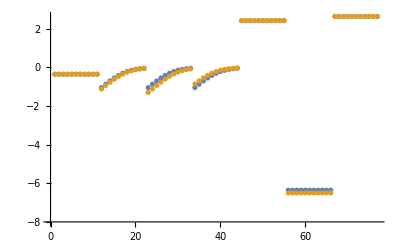

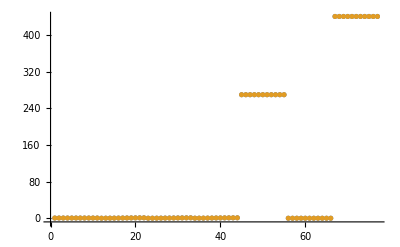

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.0000451708 | 0.37958
0.00089 | 0.000891344 | 0.150985
0.00053 | 0.000530978 | 0.184466

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 1.20456×10^-6

```mathematica
backCalculateRatios[customRatiosList[[1]][[1]], customRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 0.0000934857

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.40816 | 0.0391769